## Chapter 1

### Unit 1.1

#### 1.1.2

```mathematica
Block[{a1=0.008,a2=0.005,θ0=π/4,ϕ0=π/4,p,a3=0.2},p[θ_,ϕ_]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Graphics3D[{{Opacity[0.2],Sphere[{0,0,0},1]},{Arrowheads[0.03],Black,Arrow@Tube[{{0,0,0},1.2#},a1]&/@IdentityMatrix[3],Arrow@Tube[{{0,0,0},p[θ0,ϕ0]}]},
{Text["\!\(n\_"<>#1<>"\)",1.1#2,{0,-1.2}]}&@@@Thread@{{"x","y","z"},IdentityMatrix[3]},
{Text["\!\(0\)",p[0,0],{1.2,0}],Text["\!\(1\)",p[π,0],{1.2,0}],Text["\!\(+\)",p[π/2,0],{0,1.2}],Text["\!\(-\)",p[π/2,π],{0,1.2}],Text["\!\(ⅈ\)",p[π/2,π/2],{0,1.2}],Text["\!\(|ⅈ\&_⟩\)",p[π/2,-π/2],{0,1.2}],Text["\!\(|ψ⟩\)",p[θ0,ϕ0],{0,-1.2}]},
{Black,Glow[GrayLevel[0.7]],Table[Tube[p[θ,#]&/@Range[0,2π,π/32],a2],{θ,{π/2,θ0}}],Tube[{{0,0,0},-#},a2]&/@IdentityMatrix[3],Table[Tube[p[#,ϕ]&/@Range[0,π,π/32],a2],{ϕ,{ϕ0}}],Tube[{{0,0,0},p[π/2,ϕ0]},a2],Glow[Black],Tube[a3 p[#,ϕ0]&/@Range[0,θ0,θ0/10],a2],Tube[a3 p[π/2,#]&/@Range[0,ϕ0,ϕ0/10],a2]},{Text["θ",a3 p[θ0,ϕ0],{0,-1}],Text["ϕ",a3 p[π/2,ϕ0/2],{0,1}]}},Boxed->False,Lighting->"Neutral",ViewPoint->{5,2,2},ImageSize->200]]
```

-Graphics3D-

```mathematica
Block[{a1=0.008,a2=0.005,θ0=π/4,ϕ0=π/4,p,a3=0.2},p[θ_,ϕ_]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Graphics3D[{{Opacity[0.2],Sphere[{0,0,0},1]},{Arrowheads[0.03],Black,Arrow@Tube[{{0,0,0},1.2#},a1]&/@IdentityMatrix[3],Arrow@Tube[{{0,0,0},p[θ0,ϕ0]}]},
{Text["\!\(n\_"<>#1<>"\)",1.1#2,{0,-1.2}]}&@@@Thread@{{"x","y","z"},IdentityMatrix[3]},
{Text["\!\(↑\)",p[0,0],{1.2,0}],Text["\!\(↓\)",p[π,0],{1.2,0}],Text["\!\(→\)",p[π/2,0],{0,1.2}],Text["\!\(←\)",p[π/2,π],{0,1.2}],Text["\!\(ⅈ\)",p[π/2,π/2],{0,1.2}],Text["\!\(|ⅈ\&_⟩\)",p[π/2,-π/2],{0,1.2}],Text["\!\(|n,+⟩\)",p[θ0,ϕ0],{0,-1.2}]},
{Black,Glow[GrayLevel[0.7]],Table[Tube[p[θ,#]&/@Range[0,2π,π/32],a2],{θ,{π/2,θ0}}],Tube[{{0,0,0},-#},a2]&/@IdentityMatrix[3],Table[Tube[p[#,ϕ]&/@Range[0,π,π/32],a2],{ϕ,{ϕ0}}],Tube[{{0,0,0},p[π/2,ϕ0]},a2],Glow[Black],Tube[a3 p[#,ϕ0]&/@Range[0,θ0,θ0/10],a2],Tube[a3 p[π/2,#]&/@Range[0,ϕ0,ϕ0/10],a2]},{Text["θ",a3 p[θ0,ϕ0],{0,-1}],Text["ϕ",a3 p[π/2,ϕ0/2],{0,1}]}},Boxed->False,Lighting->"Neutral",ViewPoint->{5,2,2},ImageSize->200]]
```

-Graphics3D-

### Unit 1.2

#### 1.2.1

```mathematica
Block[{a=0.5,b=1,lt=0.4,h=1,l=3,z=0.5,c=1,spin},
spin[col_,n_]:=Block[{r=0.1,s=0.5},{{col,Arrowheads[0.03],Arrow[Tube[s{-0.5n,n}],0.1]},{Gray,Sphere[{0,0,0},r]}}];
Graphics3D[{Translate[{Lighter[#1,lt],EdgeForm[AbsoluteThickness[1]],Cuboid[{-a,-b,-a},{a,b,a}],{White,Text[Style[#3,18,Bold,FontFamily->"Arial Black"],{a,0,0}]}},{0,0,#2h}]&@@@{{Blue,-1,"N"},{Red,1,"S"}},
{Black,Scale[Tube[BSplineCurve[{{0,-l,0},{0,-l/2,0},{0,0,0},{0,l/2,z/2},{0,l,z}}],0.02],{1,1,#},{0,0,0}]&/@{1,-1}},
Translate[spin[Purple,{1,0,0}],{0,-0.8l,0}],Translate[spin[Blue,{0,0,1}],{0,0.7l,0.7 z}],Translate[spin[Red,{0,0,-1}],{0,0.7l,-0.7 z}],
Translate[{Glow[White],Polygon[{{-c,0,-c},{-c,0,c},{c,0,c},{c,0,-c}}]},{0,l,0}],Translate[{Black,Arrowheads[0.03],{Arrow[Tube[{{0,0,0},0.8#1},0.02]],Text["\!\("<>#2<>"\)",#1]}&@@@{{{1,0,0},"x"},{{0,1,0},"y"},{{0,0,1},"z"}}},{0,-1.5l,0}]},Boxed->False,ViewPoint->{5, -3,2},Lighting->"Neutral",ImageSize->300]]
```

-Graphics3D-

### Unit 2.3

#### 2.3.1 Exchange Topology

```mathematica
Block[{a=0.05,b=0.015,c=0.04,path},
path[ϕ_]:=Rotate[{Blend[{Red,Purple,Blue},ϕ/π],{EdgeForm[None],Cone[{2#,1,0}&/@{c,-c},c]},Tube[Table[{Cos[θ],Sin[θ],0},{θ,0.,π,π/32}],b]},ϕ,{1,0,0},{0,0,0}];
Graphics3D[{{Opacity[0.2],EdgeForm[LightGray],Polygon[1.5{{-1,-1,0},{-1,1,0},{1,1,0},{1,-1,0}}]},{Black,Sphere[{#,0,0},a]&/@{-1,0,1}},
path[0],path[π],{Opacity[0.2],path/@(Range[1,5]π/6)},Text["\!\(a\)",{0,0,0},{0,1}],Text["\!\(b\)",{1,0,0},{0,1}]},Boxed->False,Lighting->"Neutral"]]
```

-Graphics3D-

#### 2.3.1 Braid Group

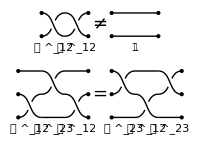

```mathematica
Block[{braid},
braid[ids_,n_]:=Block[{sigma},
sigma[i_]:=Block[{f},
f=BSplineFunction[Table[{x,Piecewise[{{0,x<0.2},{1,x>0.8}},0.5(Tanh[5(x-0.5)]+1)]},{x,0,1,0.1}]];
{Translate[Line[{#,0}&/@{0,1}],{0,#}]&/@Complement[Range[n],{i,i+1}],If[i>0,Translate[{{Line[f/@Range[0,0.4,0.02]],Line[f/@Range[0.6,1,0.02]]},Scale[Line[f/@Range[0,1,0.02]],{1,-1},{0.5,0.5}]},{0,i}]]}];{MapIndexed[Translate[{sigma[#1],Text[If[#1>0,StringTemplate["\!\(𝒫\&^\_\(`1``2`\)\)"][#1,#1+1],""],{0.5,0.5}]},{First@#2,0}]&,ids],Translate[Point[{1,#}&/@Range[n]],{#,0}]&/@{0,Length[ids]}}];
Graphics[{Translate[{Translate[braid[{1,1},2],{-3.5,0}],Text[Style["\!\(≠\)",18],{0,1.5}],Text["\!\(𝟙\)",{1.5,0.5}],Translate[braid[{-1,-1},2],{-0.5,0}]},{0,3.5}],
Translate[{Translate[braid[{1,2,1},3],{-4.5,0}],Text[Style["\!\(=\)",18],{0,2}],Translate[braid[{2,1,2},3],{-0.5,0}]},{0,0}]},PlotRangePadding->Scaled[.05],ImageSize->200]
]
```

### Unit 3.1

#### 3.1.1 Reflection

```mathematica
Block[{hf=0.05,θ=π/3},
Graphics[{{Red,AbsoluteThickness[2],Arrowheads[{{0.06,0.55}}],Arrow[ReIm@{ⅈ Exp[ⅈ θ],0}],Arrow[ReIm@{0,ⅈ Exp[-ⅈ θ]}]},{{HatchFilling[],Rectangle[{-1,0},{1,-hf}]},Line[{#,0}&/@{-1,1}]},{AbsoluteThickness[1],{Dashed,Line[ReIm@{0,0.3ⅈ}]},Circle[{0,0},0.15,{π/2,π/2+θ}],Circle[{0,0},0.14,{π/2,π/2-θ}],Circle[{0,0},0.16,{π/2,π/2-θ}],Text["\!\(θ\_1\)",ReIm[0.25 ⅈ Exp[ⅈ θ/2]]],Text["\!\(θ\_2\)",ReIm[0.25 ⅈ Exp[-ⅈ θ/2]]],Text["\!\(n\)",{1,0},{1,-1}]}},ImageSize->180]]
```

-Graphics-

#### 3.1.1 Refraction

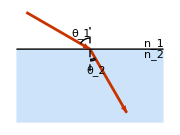

```mathematica
Block[{hf=0.05,θ1=π/3,θ2=π/6},
Graphics[{{Lighter[Blue,0.8],Rectangle[{-1,0},{1,-1}]},{Red,AbsoluteThickness[2],Arrowheads[{{0.06,0.55}}],Arrow[ReIm@{ⅈ Exp[ⅈ θ1],0}],Arrow[ReIm@{0,-ⅈ Exp[ⅈ θ2]}]},{Line[{#,0}&/@{-1,1}]},{AbsoluteThickness[1],{Dashed,Line[ReIm@{-0.3ⅈ,0.3ⅈ}]},Circle[{0,0},0.15,{π/2,π/2+θ1}],Circle[{0,0},0.14,-{π/2,π/2-θ2}],Circle[{0,0},0.16,-{π/2,π/2-θ2}],Text["\!\(θ\_1\)",ReIm[0.25 ⅈ Exp[ⅈ θ1/2]]],Text["\!\(θ\_2\)",ReIm[-0.3ⅈ Exp[ⅈ θ2/2]]],Text["\!\(n\_1\)",{1,0},{1,-1}],Text["\!\(n\_2\)",{1,0},{1,1}]}},ImageSize->180]]
```